#### Problem 1

```mathematica
r[t_]:={t^3,3t,t^4}
```

```mathematica
norm=Coefficient[Det[{{x,y,z}-r[t],r'[t],r''[t]}],#]&/@{x,y,z}
```

{36 t^2,-12 t^4,-18 t}

```mathematica
Solve[norm=={6,-2,-2}k,{k,t}]
```

{{k→0,t→0}}

no valid solution, therefore such point doesn’t exist.

#### Problem 2

```mathematica
(* 1 *)
```

```mathematica
r2[t_]:={Cos[t]/(√2),-Sin[t],Cos[t]/(√2)};
Simplify[alpha=Normalize[r2'[t]],t∈Reals];
Simplify[tan =r2'[t],t∈Reals]
Simplify[biNorm=Normalize[Cross[r2'[t],r2''[t]]],t∈Reals]
Simplify[mainNorm=Cross[biNorm,alpha],t∈Reals]
```

{-Sin[t]/(√2),-Cos[t],-Sin[t]/(√2)}

{1/(√2),0,-1/(√2)}

{-Cos[t]/(√2),Sin[t],-Cos[t]/(√2)}

```mathematica
(* 2 *)
```

```mathematica
r3[t_]:={t^3,3t,t^4}
arg=Solve[r3'[t]=={6,6,-8}k,{t,k}]
```

{{t→-1,k→1/2}}

```mathematica
r3[t]/.arg
```

{{-1,-3,1}}

```mathematica
(* 3 *)
```

```mathematica
r4[t_]:={3 Cos[t],5Sin[t]}
```

```mathematica
radius[t_]:=Simplify[Norm[r4'[t]]^3/Det[{r4'[t],r4''[t]}],t∈Reals]
```

```mathematica
center[t_]:=Normalize[Cross[r4'[t]]]*radius[t]+r4[t]
```

```mathematica
radius[Pi/4]
center[Pi/4]
```

(17 √17)/15

{-(4 √2)/3,(4 √2)/5}

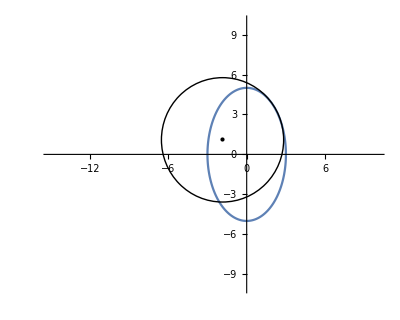

```mathematica
ParametricPlot[r4[t],{t,0,2Pi},Epilog->{Circle[center[Pi/4],radius[Pi/4]],Point[center[Pi/4]]},PlotRange->{{-15,10},{-10,10}}]
```

#### Problem 3

```mathematica
r5[t_]:={2t^2,2/3 t^3-2t}
```

```mathematica
a5[t_]:=r5''[t]
```

```mathematica
(* Tangential *) Simplify[Projection[a5[t],r5'[t]],t∈Reals]
(* Normal *) Simplify[Projection[a5[t],Cross[r5'[t]]],t∈Reals]
% + %%==a5[t]//Simplify
```

{(8 t^2)/(1+t^2),(4 t (-1+t^2))/(1+t^2)}

{(4-4 t^2)/(1+t^2),(8 t)/(1+t^2)}

True

#### Problem 4

```mathematica
(* 3 *)
```

```mathematica
r5[t_]:={3Cos[t],3Sin[t],t}
```

```mathematica
res=Integrate[Norm[r5'[t]]Det[{r4'[t],r4''[t]}]/Norm[r4'[t]]^3,{t,0,4Pi}]
```

8/3 √10 EllipticE[16/25]

```mathematica
res//N
```

10.7631